## Decouple Feedforward from Feedback (continuous case), Prob. 3.8

Goal is to implement feedforward in a way that decouples its actions from the feedback controller.

Here, we use continuous design. A discrete version is in the Discrete chapter....

```mathematica
Clear["Global`*"];
SetOptions[Plot,PlotRange -> All];
tmax=20;trange={t,0,tmax};imp=DiracDelta[t-12]; (* imp = input disturbance *)
step=UnitStep[t-1]; 
G=1/(s^2+1); Gtf=TransferFunctionModel[G,s]; y0=OutputResponse[Gtf,imp,trange]; (* open-loop impulse resp. *)
```

Design PD feedback controller K(s)

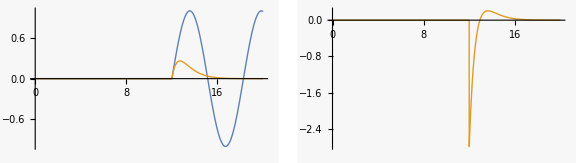

```mathematica
K1=Kp+Kd s; SG1=Together[G/(1+K1 G)]; SG1tf=TransferFunctionModel[SG1,s];
negT1=Together[(-K1 G)/(1+K1 G)]; negT1tf=TransferFunctionModel[negT1,s];
 y1=OutputResponse[SG1tf/.{Kp->1,Kd->2 √2},imp,trange] ;
u1=OutputResponse[negT1tf/.{Kp->1,Kd->2 √2},imp,trange] ;
p1=Plot[{y0,y1},{t,0,tmax}];
p2=Plot[{,u1},{t,0,tmax}];
GraphicsRow[{p1,p2 },ImageSize->Large]
```

```mathematica
OutputResponse[SG1tf/.{Kp->1,Kd->2 √2},imp,t]//Simplify//TraditionalForm
```

{ⅇ^(-√2 (t-12)) (t-12) t-12}

```mathematica
eqs1={y''[t]+y[t]==-Kp y[t]-Kd y'[t]+imp,y[0]==0,y'[0]==0}/.Kd->2 √(Kp+1);
{ysol,usol}=DSolveValue[eqs1,{y[t],-Kp y[t]-Kd y'[t]}/.Kd->2 √(Kp+1),t]//Simplify;TraditionalForm [{ysol,usol}/.Kp->1,]
```

TraditionalForm[{ⅇ^(-√2 (-12+t)) (-12+t) HeavisideTheta[-12+t],-ⅇ^(-√2 (-12+t)) (36+2 √2-3 t) HeavisideTheta[-12+t]},Null]

Design feedforward filter F(s)

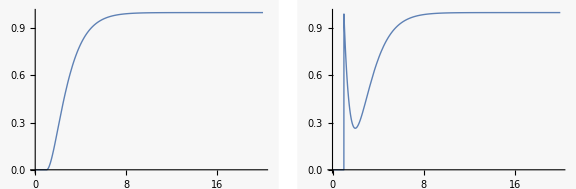

```mathematica
F=1/G 1/(1+s)^2; Ftf=TransferFunctionModel[F,s];
FGtf=TransferFunctionModel[F G,s];
rfg1=OutputResponse[FGtf,step,trange] ;
rf1=OutputResponse[Ftf,step,trange] ;
GraphicsRow[{Plot[rfg1,{t,0,tmax}], 
Plot[rf1,{t,0,tmax},PlotRange->{0,1}]},ImageSize->Large]
```

```mathematica
OutputResponse[FGtf,step,t][[1]]//TraditionalForm
```

ⅇ^-t (ⅇ^t-ⅇ t) t-1

Combine feedforward and feedback filters in a time-domain simulation

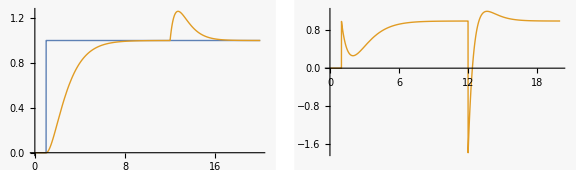

```mathematica
FFBtf=TransferFunctionModel[{F G ,SG1},s];
utf=TransferFunctionModel[{F ,negT1},s];
y3=OutputResponse[FFBtf/.{Kp->1,Kd->2 √2},{step,imp},trange] ;
u3=OutputResponse[utf/.{Kp->1,Kd->2 √2},{step,imp},trange] ;
p3=Plot[{UnitStep[t-1],y3},{t,0,tmax},Exclusions->None];
p4=Plot[{,u3},{t,0,tmax},Exclusions->None];
GraphicsRow[{p3,p4},ImageSize->Large]
```

Alternate method (draws on time-domain formulation)

```mathematica
rf=OutputResponse[Ftf,step,t][[1]] //Simplify
```

ⅇ^-t (ⅇ^t-2 ⅇ (-1+t)) UnitStep[-1+t]

```mathematica
rfg=OutputResponse[FGtf,step,t][[1]]//Simplify
```

ⅇ^-t (ⅇ^t-ⅇ t) UnitStep[-1+t]

```mathematica
rfg1=D[rfg,t][[1]]//Simplify;
```

```mathematica
y4=OutputResponse[Gtf,rf,t] //Simplify
```

{ⅇ^-t (ⅇ^t-ⅇ t) UnitStep[-1+t]}

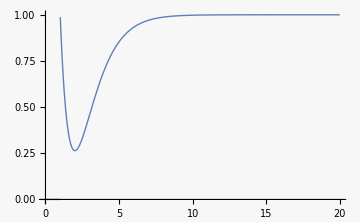

```mathematica
Plot[rf,{t,0,tmax}]
```

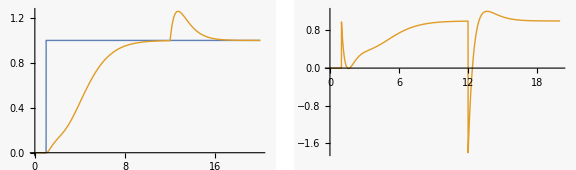

```mathematica
eqs2={y''[t]+y[t]==rf+Kp(rfg- y[t])+Kd (rfg1-y'[t])+imp,y[0]==0,y'[0]==0}//.{Kd->2 √(Kp+1),Kp->1};
{ysol1,usol1}=DSolveValue[eqs2,{y[t],Kp(rfg- y[t])+Kd (rfg1-y'[t])}//.{Kd->2 √(Kp+1),Kp->1},t];
usol1a=usol1+rf;

GraphicsRow[{Plot[{step,ysol1},{t,0,tmax},Exclusions->None],Plot[{,usol1a},{t,0,tmax},Exclusions->None]},ImageSize->Large]
```

Export data.

```mathematica
dt=0.01;
dat = Table[{ysol1//N,usol1a//N},{t,0,tmax,dt}];
(* 
SetDirectory[NotebookDirectory[]];Export["feedforward-feedback.dat", dat];
*)
```